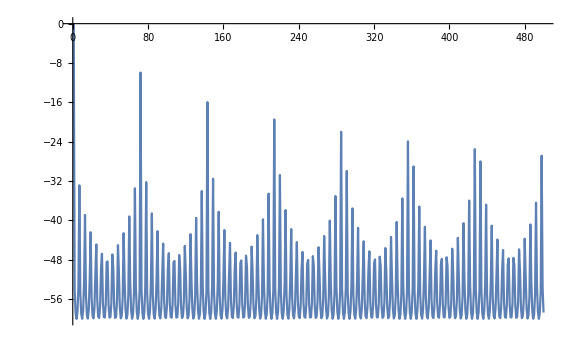

```mathematica
r:=1000;
T:=1/r;
f:=71;
s:=Table[SawtoothWave[f t],{t,0,1-T,T}];
spec:=Abs@Take[Fourier[s],Floor@r/2];
spec=spec/Max[spec];
ListPlot[20Log10@spec,PlotRange->{{0,Floor@r/2},{-60,0}},Joined->True,ImageSize->Large]
```

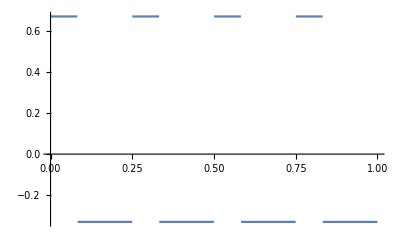

```mathematica
f=4;
p =.33;
Plot[SawtoothWave[f t-p]-SawtoothWave[f t],{t,0,1}]
```